```mathematica
Quit
```

# Collinear Factorize

## Choose Pair

```mathematica
ForwardChoice=1;
ConjugateChoice=2;
```

## Load Card

```mathematica
CardName="UU"
```

## Initialization

```mathematica
Get[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"Addon","Load","LoadFACET.wl"}]];
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynCalcLegacy 1.0.0

FeynCalcLegacy contains legacy functions and symbols that were removed in FeynCalc 10.2.1

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynFacet 0.1

## Setup

```mathematica
Setup=Get[FileNameJoin[{NotebookDirectory[],"Cards",CardName<>".wl"}]];
Setup["CardName"]=CardName;
Setup["ForwardAmplitudes","SelectedIndex"]=ForwardChoice;
Setup["ConjugateAmplitudes","SelectedIndex"]=ConjugateChoice;
```

## Factorization, Partial Fraction, Dimensional Shift, and Tarasov Recurrence

Forward 1

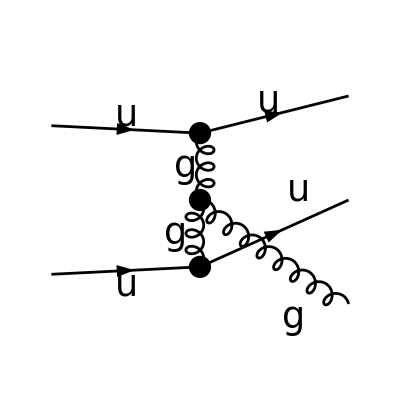

Conjugate 2

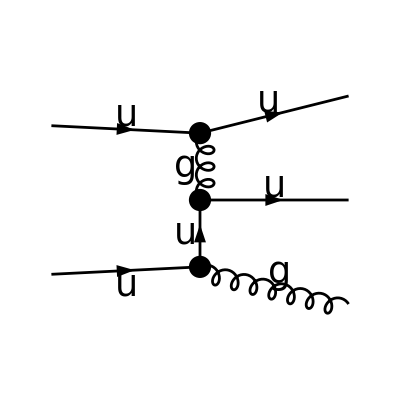

Topology | External momenta | Cut indices | Cut directions
TopologyF1C2N1 | {ka,kb,kc} | {3,1} | {1,1}
TopologyF1C2N2 | {ka,kb,kc} | {3,1} | {1,1}

Master integrals | Size (kB)
12 | 1929.54

```mathematica
{FractionMeasure,PreFactor,PhaseSpace,Integrand,Topologies}=CollinearFactorizePreIBP[Setup];
```

```mathematica
FractionMeasure
```

ⅆxa ⅆxb ⅆzh

```mathematica
PreFactor//TraditionalForm
```

(ⅈ αs^3 2^(8-D) π^(5-D/2) C_A^2 C_F f1(xb) h1(xa) H1(zh) (n·Pb) (nb·Pa) (nhb·Ph))/(zh^3 (ka-kc)^4)

```mathematica
PhaseSpace//TraditionalForm
```

-ⅈ π^(-D/2) (d^D ke)

```mathematica
Integrand
```

## Save

```mathematica
Result=GenerateCollinearFactorizePreIBPResult[Setup,FractionMeasure,PreFactor,PhaseSpace,Integrand,Topologies];
SaveCollinearFactorizePreIBPResult[Result]
```